```mathematica
projectDir=FileNameJoin[{$HomeDirectory,"Documents","physics-informed-financial-ml"}];
raw=Import[FileNameJoin[{projectDir,"data","raw","SP500_2011_2026.csv"}],"CSV"];
data=Rest[raw];

dates=DateObject[{#,{"Year","-","Month","-","Day"}},"Day"]&/@data[[All,1]];
closeP=data[[All,5]];
r=Differences[Log[closeP]];
rDates=Rest[dates];

{Length[closeP],Length[r],First[rDates],Last[rDates]}
{r[[1]],Mean[r],StandardDeviation[r]}
```

{3772,3771,Mon 4 Apr 2011,Wed 1 Apr 2026}

{0.000345179,0.000423318,0.010927}

{3771,3771,3771,3771}

{4,21,19}

{0.00482945,0.00482945}

{0.0259194,0.0259194}

{0.00557322,0.00557322}

{0.010939,0.010927}

{Fri 27 Mar 2020,0.0616693}

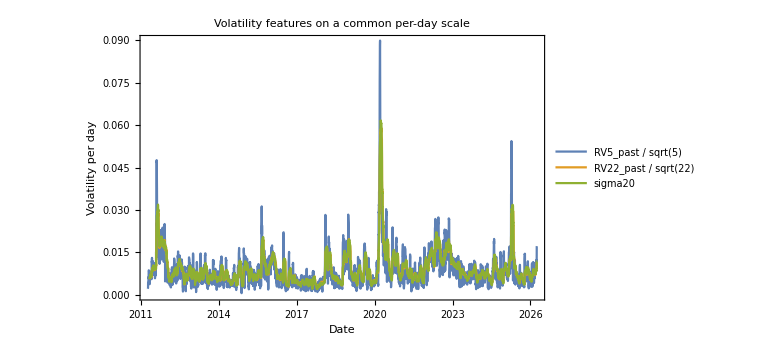

```mathematica
n=Length[r];
pad[k_,f_]:=Join[ConstantArray[Missing["WarmUp"],k-1],Table[f[t],{t,k,n}]];

absR=Abs[r];
rv5=pad[5,Sqrt[Total[r[[#-4;;#]]^2]]&];
rv22=pad[22,Sqrt[Total[r[[#-21;;#]]^2]]&];
sig20=pad[20,StandardDeviation[r[[#-19;;#]]]&];

Length/@{absR,rv5,rv22,sig20}
Count[#,_Missing]&/@{rv5,rv22,sig20}

{rv5[[5]],0.00482945}
{rv22[[22]],Sqrt[Total[r[[1;;22]]^2]]}
{sig20[[20]],Sqrt[Total[(r[[1;;20]]-Mean[r[[1;;20]]])^2]/19]}

{Sqrt[Mean[DeleteMissing[rv22]^2]/22],StandardDeviation[r]}
{rDates[[First@Ordering[sig20/. _Missing->0,-1]]],Max[DeleteMissing[sig20]]}

ts[v_,s_]:=TimeSeries[Select[Transpose[{rDates,v/s}],NumericQ[#[[2]]]&]];
pVol=DateListPlot[{ts[rv5,Sqrt[5]],ts[rv22,Sqrt[22]],ts[sig20,1]},PlotLegends->{"RV5_past / sqrt(5)","RV22_past / sqrt(22)","sigma20"},PlotRange->All,ImageSize->Large,FrameLabel->{"Date","Volatility per day"},PlotLabel->"Volatility features on a common per-day scale"]
Export[FileNameJoin[{projectDir,"results","figures","07_volatility_features.png"}],pVol];
```

{3771,3771,3771}

{1,2,9}

{Wed 24 Aug 2011,0.0337102,Tue 23 Aug 2011,0.0337102}

{Wed 24 Aug 2011,0.000258082,Mon 22 Aug 2011,0.000258082}

{-0.00960005,-0.00960005}

1.8336×10^-15

{Wed 18 Mar 2020,-0.266395}

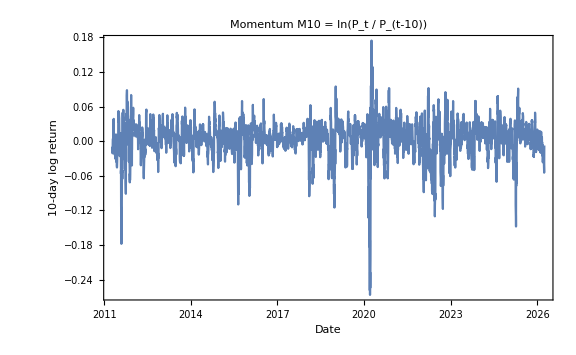

```mathematica
rLag1=Join[{Missing["WarmUp"]},Most[r]];
rLag2=Join[ConstantArray[Missing["WarmUp"],2],Drop[r,-2]];
m10=pad[10,Total[r[[#-9;;#]]]&];

Length/@{rLag1,rLag2,m10}
Count[#,_Missing]&/@{rLag1,rLag2,m10}

{rDates[[100]],rLag1[[100]],rDates[[99]],r[[99]]}
{rDates[[100]],rLag2[[100]],rDates[[98]],r[[98]]}

{m10[[10]],Log[closeP[[11]]/closeP[[1]]]}
Max[Abs[DeleteMissing[m10]-Table[Log[closeP[[t+1]]/closeP[[t-9]]],{t,10,n}]]]

{rDates[[First@Ordering[m10/. _Missing->0,1]]],Min[DeleteMissing[m10]]}

pMom=DateListPlot[ts[m10,1],PlotRange->All,ImageSize->Large,FrameLabel->{"Date","10-day log return"},PlotLabel->"Momentum M10 = ln(P_t / P_(t-10))"]
Export[FileNameJoin[{projectDir,"results","figures","08_momentum.png"}],pMom];
```

```mathematica
target=Join[Table[Sqrt[Total[r[[t+1;;t+5]]^2]],{t,1,n-5}],ConstantArray[Missing["NoFuture"],5]];

cols={"Date","Close","r","r_lag1","r_lag2","abs_r","RV5_past","RV22_past","sigma20","M10","RV5_target"};
rowIdx=Range[22,n-5];
ds=Table[{rDates[[t]],closeP[[t+1]],r[[t]],rLag1[[t]],rLag2[[t]],absR[[t]],rv5[[t]],rv22[[t]],sig20[[t]],m10[[t]],target[[t]]},{t,rowIdx}];

Dimensions[ds]
{First[ds][[1]],Last[ds][[1]]}
Count[ds[[All,2;;]],x_/;!NumericQ[x],{2}]

ds[[1;;-6,11]]==ds[[6;;,7]]

old=Rest[Import[FileNameJoin[{projectDir,"data","processed","sp500_rv5_dataset.csv"}],"CSV"]];
{old[[18,1]],DateString[ds[[1,1]],"ISODate"]}
Max[Abs[Flatten[old[[18;;,{4,5}]]-ds[[All,{7,11}]]]]]
```

{3745,11}

{Wed 4 May 2011,Wed 25 Mar 2026}

0

True

{2011-05-04,2011-05-04}

0.

```mathematica
featuresFrom[p_]:=Module[{rr=Differences[Log[p]],nn,pd},nn=Length[rr];
pd[k_,f_]:=Join[ConstantArray[Missing["WarmUp"],k-1],Table[f[t],{t,k,nn}]];
{rr,Join[{Missing["WarmUp"]},Most[rr]],Join[ConstantArray[Missing["WarmUp"],2],Drop[rr,-2]],Abs[rr],pd[5,Sqrt[Total[rr[[#-4;;#]]^2]]&],pd[22,Sqrt[Total[rr[[#-21;;#]]^2]]&],pd[20,StandardDeviation[rr[[#-19;;#]]]&],pd[10,Total[rr[[#-9;;#]]]&]}];

full=featuresFrom[closeP];
full=={r,rLag1,rLag2,absR,rv5,rv22,sig20,m10}

SeedRandom[1];
cuts=Sort[Join[{22,1000,n-5},RandomSample[Range[23,n-6],25]]];
Length[cuts]

diffs=Table[Max[Abs[featuresFrom[closeP[[1;;T+1]]][[All,T]]-full[[All,T]]]],{T,cuts}];
Max[diffs]

leakyFrom[p_]:=Module[{rr=Differences[Log[p]]},Table[Mean[Abs[rr[[Max[1,t-2];;Min[Length[rr],t+2]]]]],{t,Length[rr]}]];
leakyFull=leakyFrom[closeP];
leakyDiffs=Table[Abs[leakyFrom[closeP[[1;;T+1]]][[T]]-leakyFull[[T]]],{T,cuts}];
{Count[leakyDiffs,d_/;d>0],Max[leakyDiffs]}
```

True

28

1.38778×10^-17

{28,0.00558899}

```mathematica
featNames=cols[[3;;10]];
X=ds[[All,3;;10]];
y=ds[[All,11]];

corrY=Table[{featNames[[j]],Correlation[X[[All,j]],y],SpearmanRho[X[[All,j]],y]},{j,8}];
TableForm[MapAt[Round[#,0.001]&,corrY,{All,2;;3}],TableHeadings->{None,{"Feature","Pearson","Spearman"}}]

cm=Correlation[X];
TableForm[Round[cm,0.01],TableHeadings->{featNames,featNames}]

Export[FileNameJoin[{projectDir,"results","tables","feature_target_correlations.csv"}],Prepend[corrY,{"Feature","Pearson","Spearman"}]];
Export[FileNameJoin[{projectDir,"results","tables","feature_correlation_matrix.csv"}],Prepend[MapThread[Prepend,{cm,featNames}],Prepend[featNames,""]]];
```

Feature | Pearson | Spearman
r | -0.173 | -0.147
r_lag1 | -0.18 | -0.135
r_lag2 | -0.154 | -0.123
abs_r | 0.496 | 0.322
RV5_past | 0.666 | 0.552
RV22_past | 0.593 | 0.532
sigma20 | 0.597 | 0.542
M10 | -0.458 | -0.357

| r | r_lag1 | r_lag2 | abs_r | RV5_past | RV22_past | sigma20 | M10
r | 1. | -0.12 | 0.08 | -0.1 | -0.04 | 0.01 | 0.01 | 0.32
r_lag1 | -0.12 | 1. | -0.12 | -0.12 | -0.07 | 0. | 0. | 0.25
r_lag2 | 0.08 | -0.12 | 1. | -0.15 | -0.11 | -0.01 | -0.02 | 0.31
abs_r | -0.1 | -0.12 | -0.15 | 1. | 0.68 | 0.52 | 0.52 | -0.36
RV5_past | -0.04 | -0.07 | -0.11 | 0.68 | 1. | 0.79 | 0.8 | -0.46
RV22_past | 0.01 | 0. | -0.01 | 0.52 | 0.79 | 1. | 0.99 | -0.14
sigma20 | 0.01 | 0. | -0.02 | 0.52 | 0.8 | 0.99 | 1. | -0.15
M10 | 0.32 | 0.25 | 0.31 | -0.36 | -0.46 | -0.14 | -0.15 | 1.

```mathematica
featFile=FileNameJoin[{projectDir,"data","processed","features_v1.csv"}];
Export[featFile,Prepend[Prepend[Rest[#],DateString[First[#],"ISODate"]]&/@ds,cols]];

chk=Import[featFile,"CSV"];
Dimensions[chk]
chk[[1]]==cols
{chk[[2,1]],chk[[-1,1]]}
Max[Abs[Flatten[chk[[2;;,2;;]]-ds[[All,2;;]]]]]
```

{3746,11}

True

{2011-05-04,2026-03-25}

0.